# Kebab parisiens - Données

```mathematica
lecteur=StringJoin[Take[Characters[ToString[NotebookDirectory[]]],{1,3}]];
adresse=StringJoin[Take[Characters[ToString[NotebookDirectory[]]],{4,-1}]];
```

```mathematica
dossierdata="donnees\\";
```

```mathematica
dossierref="kebab\\";
If[DirectoryQ[StringJoin[lecteur,adresse,dossierref]]==False,CreateDirectory[StringJoin[lecteur,adresse,dossierref]],];
```

## Compréhension de la structure du site internet

```mathematica
liste={
"https://www.kebab-frites.com/kebab/paris-la-defense-v45899.html",
"https://www.kebab-frites.com/kebab/paris-01-v18004.html";
"https://www.kebab-frites.com/kebab/paris-02-v45900.html",
"https://www.kebab-frites.com/kebab/paris-03-v45901.html",
"https://www.kebab-frites.com/kebab/paris-04-v45902.html",
"https://www.kebab-frites.com/kebab/paris-05-v45903.html",
"https://www.kebab-frites.com/kebab/paris-06-v45904.html",
"https://www.kebab-frites.com/kebab/paris-07-v45905.html",
"https://www.kebab-frites.com/kebab/paris-08-v45906.html",
"https://www.kebab-frites.com/kebab/paris-09-v45907.html",
"https://www.kebab-frites.com/kebab/paris-10-v45908.html",
"https://www.kebab-frites.com/kebab/paris-11-v45909.html",
"https://www.kebab-frites.com/kebab/paris-12-v45910.html",
"https://www.kebab-frites.com/kebab/paris-13-v45911.html",
"https://www.kebab-frites.com/kebab/paris-14-v45912.html",
"https://www.kebab-frites.com/kebab/paris-15-v45913.html",
"https://www.kebab-frites.com/kebab/paris-16-v45914.html",
"https://www.kebab-frites.com/kebab/paris-17-v45915.html",
"https://www.kebab-frites.com/kebab/paris-18-v45916.html",
"https://www.kebab-frites.com/kebab/paris-19-v45917.html",
"https://www.kebab-frites.com/kebab/paris-20-v45918.html"};
```

```mathematica
Do[SystemOpen[liste[[i]]];Pause[0.5],{i,1,Length[liste]}]
```

```mathematica
Clear[liste];
```

À partir des adresses de chaque arrondissement, copier-coller le nom des enseignes et leur arrondissements. Chaque mot doit être séparé d’un espace.
Exemple : Berliner Das Original Paris La Défense

## Création d’un fichier contenant les adresses U.R.L.

```mathematica
listedeskebab=Import[StringJoin[lecteur,adresse,dossierdata,"listekebab.csv"]];
```

```mathematica
(*Liste des caractères présents dans tous les mots*)
Union[Flatten[Table[Characters[listedeskebab],{i,1,Length[listedeskebab]}]]]
```

{!,&,(,),-,.,',/, ,0,1,2,3,4,5,6,7,8,9,a,A,b,B,c,ç,C,d,D,e,é,è,ê,E,f,F,g,G,h,H,i,î,ï,I,j,J,k,K,l,L,m,M,n,N,o,ö,O,Ô,p,P,q,Q,r,R,s,S,t,T,u,ü,U,Ü,v,V,w,W,x,X,y,Y,z,Z,’}

```mathematica
lettreminuscule=Alphabet[];
lettremajuscule=ToUpperCase[Alphabet[]];
listedescaracteresspeciaux={"!","&","(",")",".","'","/","’"};
lettrespeciale={"ç","é","è","ê","î","ï","ö","Ô","ü","Ü"};
lettrespecialecorrection={"c","e","e","e","i","i","i","o","u","u"};
listepb={"anatolien-paris-03","casse-croute-grec---chez-copain-paris-05","restaurant-mediterranee-paris-06","le-soleil-danatolie-paris-10","luks-kebab-paris-10","paristanbul-gare-de-lest-paris-10","restaurant-cizbiz-paris-11","sefa-antalya-paris-12","luks-kebab-paris-13","kebab-du-15eme--xveme--paris-15","kebab-des-batignolles---loriginal-paris-17","soleil-dor-paris-17","chez-karim---resto-grec-plat-algerien-paris-18","chez-salem---boulangerie-sandwich-paris-18","gemuse---berliner-kebap-paris-18","kiul-kebab-paris-18","grill-bosphore-paris-19","avs--a-votre-service--paris-19","latelier-du-kebab-paris-20","tuz-gilu-paris-20","turkish-grill--chicken-paris-20"};
listepbcorrection={"restaurant-durum-paris-03","casse-croute-grec-paris-05","restaurant-mediterranee-paris-05","le-soleil-danatolie-paris-11","lks-kebab-paris-10","paristanbul-gare-de-l-39est-paris-10","saray-paris-11","karanfil-paris-12","lks-kebab-paris-13","kebab-du-15eme-xveme-paris-15","restaurant-bodrum-paris-17","soleil-d-39or-paris-17","chez-karim-resto-grec-plat-algerien-paris-18","chez-salem-boulangerie-sandwich-paris-18","gemse-berliner-kebap-paris-18","koul-kebab-paris-18","grill-bosphore-paris-19-1","avs-a-votre-service-paris-19","l-39atelier-du-kebab-paris-20","tuz-golu-paris-20","turkish-grill-chicken-paris-20"};
adressekebab=Table[0,{i,1,Length[listedeskebab]}];
Do[
nn=n;
nomkebab=listedeskebab[[nn]];
Do[nomkebab=StringReplace[nomkebab,lettremajuscule[[i]]->lettreminuscule[[i]]],{i,1,Length[lettremajuscule]}];
Do[nomkebab=StringReplace[nomkebab,listedescaracteresspeciaux[[i]]->""],{i,1,Length[listedescaracteresspeciaux]}];
Do[nomkebab=StringReplace[nomkebab,lettrespeciale[[i]]->lettrespecialecorrection[[i]]],{i,1,Length[lettrespeciale]}];
Do[nomkebab=StringReplace[nomkebab," "-> "-"],{i,1,Length[lettrespeciale]}];
Do[If[Position[nomkebab,listepb[[i]]]≠{},nomkebab=listepbcorrection[[i]]],{i,1,Length[listepb]}];
adressekebab[[nn]]=nomkebab;
Clear[nn,nomkebab];,{n,1,Length[adressekebab]}];
Clear[lettremajuscule,lettreminuscule,listedescaracteresspeciaux,lettrespeciale,lettrespecialecorrection,listepb,listepbcorrection];
```

```mathematica
(*Vérification des U.R.L.*)
url="https://www.kebab-frites.com/kebab/";
adresseurlkebab=Table[StringJoin[url,adressekebab[[i]],".html"],{i,1,Length[adressekebab]}];
Clear[url];
Do[
If[
StringPosition[Import[adresseurlkebab[[i]],"Text"],"Erreur ! Page non trouvée !"]≠{},SystemOpen[adresseurlkebab[[i]]];Pause[0.25];
];,{i,1,Length[adressekebab]}];
```

```mathematica
Export[StringJoin[lecteur,adresse,dossierdata,"adresse-url-kebab.csv"],adresseurlkebab,CharacterEncoding->"UTF8"];
```

```mathematica
Clear[listedeskebab,adressekebab,adresseurlkebab];
```

## Scrapping

```mathematica
adresseurlkebab=Flatten[Import[StringJoin[lecteur,adresse,dossierdata,"adresse-url-kebab.csv"]]];
```

```mathematica
scrapping=Table[0,{i,1,Length[adresseurlkebab]}];
prestationspossibles={"Boissons","Burgers","Desserts","Grillades","Kebab","Lahmacun/Pide","Pizzas","Plats/Assiettes","Salades",
"Sandwichs"};
servicespossibles={"Accès handicapés","Broche faite Maison","Carte de fidélité","Certificat halal","Frîtes fraiches Maison","Groupes acceptés","Menu enfant","Pain fait Maison","Parking","Réduction étudiants","Restauration à emporter","Restauration sur place","Salle avec télévision","Salle climatisée","Service de livraison","Terrasse","Thé offert","Wifi gratuit"};
Do[
nn=n;
url=adresseurlkebab[[nn]];
Print[url];
(*SystemOpen[url];*)
data=Import[url,"Text"];
caracteres=Characters[data];
enseigne=StringJoin[Take[caracteres,{StringPosition[data,"<h1>"][[1,2]]+1,StringPosition[data,"</h1>"][[1,1]]-1}]];
adresse2=StringJoin[Take[caracteres,{StringPosition[data,"<p class=\"adresse\">"][[1,2]]+1,StringPosition[data,"</p></div><div class=\"note_avis\" id=\"scroll_avis\">"][[1,1]]-1}]];
pos=StringPosition[adresse2," - "];
adressepostale=StringJoin[Take[Characters[adresse2],{1,pos[[1,1]]-1}]];
codepostal=StringJoin[Take[Characters[adresse2],{pos[[1,2]]+1,pos[[1,2]]+5}]];
commune=StringJoin[Take[Characters[adresse2],{pos[[1,2]]+7,-1}]];
Clear[pos,adresse2];
note=StringJoin[Take[caracteres,{StringPosition[data,"<div class=\"note_avis\" id=\"scroll_avis\">"][[1,2]]+1,StringPosition[data,"avis</div></div>"][[1,1]]-1}]];
caracteresnote=Characters[note];
noteglobale=StringJoin[Take[caracteresnote,{StringPosition[note,"<div class=\"notesur note3\">"][[1,2]]+1,StringPosition[note,"</div><div>"][[1,1]]-1}]];
nbavis=StringJoin[Take[caracteresnote,{StringPosition[note,"</div><div>"][[1,2]]+1,-2}]];
Clear[note,caracteresnote];
telephone=StringJoin[Take[caracteres,{StringPosition[data,"<div class=\"tel\"><a href=\"tel:"][[1,2]]+1,StringPosition[data,"\">Appeler"][[1,1]]-1}]];
pos=Partition[Characters[telephone],2];
telephone=StringJoin[Table[If[i≠Length[pos],StringJoin[pos[[i]]," "],StringJoin[pos[[i]]]],{i,1,Length[pos]}]];
Clear[pos];
horaires=StringJoin[Take[caracteres,{StringPosition[data,"<h2 name=\"horaires\" class=\"opened\">Horaires</h2><dl  class=\"dis\" data-value=\"visible\"id=\"depli_horaires\">"][[1,2]]+1,StringPosition[data,"</section><section class=\"depli\"><h2 name=\"prestations\" class=\"opened\">"][[1,1]]-1}]];
horaires=Partition[Cases[StringSplit[horaires,{"<dt>","<span><span></dt>","<dd><span></span>","</dd>","</dl>"}],Except[""]],2];
horaireslundi=horaires[[1,2]];
horairesmardi=horaires[[2,2]];
horairesmercredi=horaires[[3,2]];
horairesjeudi=horaires[[4,2]];
horairesvendredi=horaires[[5,2]];
horairessamedi=horaires[[6,2]];
horairesdimanche=horaires[[7,2]];
Clear[horaires];
prestations=StringJoin[Take[caracteres,{StringPosition[data,"<section class=\"depli\"><h2 name=\"prestations\" class=\"opened\">Prestations</h2>"][[1,2]]+1,StringPosition[data,"</section><section class=\"depli\"><h2 name=\"services\" class=\"opened\">"][[1,1]]-1}]];
If[StringPosition[prestations,"<li>"]≠{},
pos1=Transpose[StringPosition[prestations,"<li>"]][[2]]+1;
pos2=Transpose[StringPosition[prestations,"</li>"]][[1]]-1;
pos=Table[pos1[[i]]-pos2,{i,1,Length[pos1]}];
pos2=Table[pos2[[Position[Table[If[pos[[i,j]]≤0,"Vrai","Faux"],{j,1,Length[pos[[i]]]}],"Vrai"][[1,1]]]],{i,1,Length[pos]}];
Clear[pos];
prestationspresentes=Table[StringJoin[Take[Characters[prestations],{pos1[[i]],pos2[[i]]}]],{i,1,Length[pos1]}];
Clear[pos1,pos2];,
prestationspresentes={};
];
If[prestationspresentes≠{},
prestationsnonpresentes=Complement[prestationspossibles,prestationspresentes];
prestations=Table["NON",{i,1,Length[prestationspossibles]}];
pos=Flatten[Table[Position[prestationspossibles,prestationspresentes[[i]]],{i,1,Length[prestationspresentes]}]];
Do[prestations[[pos[[i]]]]="OUI",{i,1,Length[pos]}];
Clear[pos,prestationsnonpresentes];,
prestations=Table["n.c.",{i,1,Length[prestationspossibles]}];
];
Clear[prestationspresentes];
services=StringJoin[Take[caracteres,{StringPosition[data,"<section class=\"depli\"><h2 name=\"services\" class=\"opened\">Services</h2>"][[1,2]]+1,StringPosition[data,"</section><section class=\"depli\"><h2 name=\"tarifs\" class=\"opened\">Tarifs</h2>"][[1,1]]-1}]];
If[StringPosition[services,"<li>"]≠{},
pos1=Transpose[StringPosition[services,"<li>"]][[2]]+1;
pos2=Transpose[StringPosition[services,"</li>"]][[1]]-1;
pos=Table[pos1[[i]]-pos2,{i,1,Length[pos1]}];
pos2=Table[pos2[[Position[Table[If[pos[[i,j]]≤0,"Vrai","Faux"],{j,1,Length[pos[[i]]]}],"Vrai"][[1,1]]]],{i,1,Length[pos]}];
Clear[pos];
servicespresents=Table[StringJoin[Take[Characters[services],{pos1[[i]],pos2[[i]]}]],{i,1,Length[pos1]}];
Clear[pos1,pos2];,
servicespresents={};
];
If[servicespresents≠{},
servicesnonpresents=Complement[servicespossibles,servicespresents];
services=Table["NON",{i,1,Length[servicespossibles]}];
pos=Flatten[Table[Position[servicespossibles,servicespresents[[i]]],{i,1,Length[servicespresents]}]];
Do[services[[pos[[i]]]]="OUI",{i,1,Length[pos]}];
Clear[pos,servicesnonpresents];,
services=Table["n.c.",{i,1,Length[servicespossibles]}];
];
Clear[servicespresents];
tarifs=StringJoin[Take[caracteres,{StringPosition[data,"<section class=\"depli\"><h2 name=\"tarifs\" class=\"opened\">Tarifs</h2>"][[1,2]]+1,StringPosition[data,"</section><section class=\"depli\"><h2 name=\"photos\" class=\"opened\">Photos</h2>"][[1,1]]-1}]];
caracterestarifs=Characters[tarifs];
tarifs=StringJoin[Take[caracterestarifs,{StringPosition[tarifs,"<li class=\"noico\">"][[1,2]]+1,StringPosition[tarifs,"</li></ul>"][[1,1]]-1}]];
Clear[caracterestarifs];
If[StringPosition[tarifs,"<b>"]≠{},
tarifs=Cases[StringSplit[tarifs,{"<b>","</b>","<dl><dt>","<span></span></dt><dd><span></span>","</dd></dl>","</li><li class=\"noico\">","</dd><dt>"}],Except[""]],
];
notesdetaillees=StringJoin[Take[caracteres,{StringPosition[data,"</section><section class=\"depli last\"><h2 id=\"scroll_avis_target\" name=\"note_detail\" class=\"opened\">Notes détaillées</h2>"][[1,2]]+1,StringPosition[data,"</section><section class=\"avis\">"][[1,1]]-1}]];
caracteresnotesdetaillees=Characters[notesdetaillees];
pos1=Flatten[{StringPosition[notesdetaillees,"<li><div>Accueil</div><div class=\"stars\"><div class=\"s"][[1,2]],StringPosition[notesdetaillees,"<li><div>Hygiène</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Fraicheur</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Crudités</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Sauces</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Viandes</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Frites</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Pain</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Quantité</div><div class=\"stars\"><div class=\"s"][[1,2]],
StringPosition[notesdetaillees,"<li><div>Qualité/prix</div><div class=\"stars\"><div class=\"s"][[1,2]]},1]+1;
pos2=Transpose[StringPosition[notesdetaillees,"\"></div></div></li>"]][[1]]-1;
notesdetaillees=Table[StringJoin[Take[caracteresnotesdetaillees,{pos1[[i]],pos2[[i]]}]],{i,1,Min[Length[pos1],Length[pos2]]}];
accueil=notesdetaillees[[1]];
hygiene=notesdetaillees[[2]];
fraicheur=notesdetaillees[[3]];
crudites=notesdetaillees[[4]];
sauces=notesdetaillees[[5]];
viandes=notesdetaillees[[6]];
frites=notesdetaillees[[7]];
pain=notesdetaillees[[8]];
quantite=notesdetaillees[[9]];
qualiteprix=notesdetaillees[[10]];
Clear[notesdetaillees,caracteresnotesdetaillees,pos1,pos2];
scrapping[[nn]]=Flatten[{url,enseigne,adressepostale,codepostal,commune,telephone,noteglobale,nbavis,horaireslundi,horairesmardi,horairesmercredi,horairesjeudi,horairesvendredi,horairessamedi,horairesdimanche,prestations,services,tarifs,accueil,hygiene,fraicheur,crudites,sauces,viandes,frites,pain,quantite,qualiteprix}];
Clear[data,url,enseigne,adressepostale,codepostal,commune,telephone,noteglobale,nbavis,horaireslundi,horairesmardi,horairesmercredi,horairesjeudi,horairesvendredi,horairessamedi,horairesdimanche,prestations,services,tarifs,accueil,hygiene,fraicheur,crudites,sauces,viandes,frites,pain,quantite,qualiteprix];
Clear[nn];,{n,1,Length[scrapping]}];
```

https://www.kebab-frites.com/kebab/berliner-das-original-paris-la-defense.html

https://www.kebab-frites.com/kebab/nabab-kebab-paris-01.html

https://www.kebab-frites.com/kebab/al-boustan-paris-01.html

https://www.kebab-frites.com/kebab/cartage-ii-paris-01.html

https://www.kebab-frites.com/kebab/pita-kabab-paris-01.html

https://www.kebab-frites.com/kebab/marmaris-paris-01.html

https://www.kebab-frites.com/kebab/le-bosphore-paris-01.html

https://www.kebab-frites.com/kebab/chez-alexandre-paris-01.html

https://www.kebab-frites.com/kebab/restaurant-zam-zam-paris-01.html

https://www.kebab-frites.com/kebab/delices-des-halles-paris-01.html

https://www.kebab-frites.com/kebab/istambul-paris-01.html

https://www.kebab-frites.com/kebab/fallafel-chatelet-paris-01.html

https://www.kebab-frites.com/kebab/grill-burger-paris-01.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-01.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-01-1.html

https://www.kebab-frites.com/kebab/sultan-paris-01.html

https://www.kebab-frites.com/kebab/baobab-paris-01.html

https://www.kebab-frites.com/kebab/le-baal-paris-01.html

https://www.kebab-frites.com/kebab/kebab-paradise-paris-01.html

https://www.kebab-frites.com/kebab/madrevo-paris-02.html

https://www.kebab-frites.com/kebab/grille-paris-02.html

https://www.kebab-frites.com/kebab/mimosa-paris-02.html

https://www.kebab-frites.com/kebab/paristanbul-paris-02.html

https://www.kebab-frites.com/kebab/st-eustache-chawarma-paris-02.html

https://www.kebab-frites.com/kebab/restaurant-dilan-paris-02.html

https://www.kebab-frites.com/kebab/tubigo-sandwich-paris-02.html

https://www.kebab-frites.com/kebab/opera-food-paris-02.html

https://www.kebab-frites.com/kebab/orient-express-2-paris-02.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-02.html

https://www.kebab-frites.com/kebab/broche-paris-02.html

https://www.kebab-frites.com/kebab/niekebab-paris-02.html

https://www.kebab-frites.com/kebab/restaurant-lider-paris-02.html

https://www.kebab-frites.com/kebab/restaurant-evan-paris-02.html

https://www.kebab-frites.com/kebab/la-boule-paris-02.html

https://www.kebab-frites.com/kebab/so-fresh-paris-02.html

https://www.kebab-frites.com/kebab/allokeb-paris-02.html

https://www.kebab-frites.com/kebab/les-grillades-du-desert-paris-02.html

https://www.kebab-frites.com/kebab/saz-paris-02.html

https://www.kebab-frites.com/kebab/filakia-paris-02.html

https://www.kebab-frites.com/kebab/restaurant-durum-paris-03.html

https://www.kebab-frites.com/kebab/hak-yolu-restaurant-paris-03.html

https://www.kebab-frites.com/kebab/king-sandwich-paris-03.html

https://www.kebab-frites.com/kebab/restaurant-pachamanca-paris-03.html

https://www.kebab-frites.com/kebab/omer-kebab-paris-03.html

https://www.kebab-frites.com/kebab/suite-au-kebab-paris-03.html

https://www.kebab-frites.com/kebab/caspienne-food-paris-03.html

https://www.kebab-frites.com/kebab/las-du-fallafel-paris-04.html

https://www.kebab-frites.com/kebab/mi-va-mi-paris-04.html

https://www.kebab-frites.com/kebab/le-saint-paul-paris-04.html

https://www.kebab-frites.com/kebab/pitzman-paris-04.html

https://www.kebab-frites.com/kebab/snack-la-goulette-paris-04.html

https://www.kebab-frites.com/kebab/shawarma-lovers-paris-04.html

https://www.kebab-frites.com/kebab/food-and-drinks-paris-04.html

https://www.kebab-frites.com/kebab/mickys-deli-paris-04.html

https://www.kebab-frites.com/kebab/king-falafel-palace-paris-04.html

https://www.kebab-frites.com/kebab/casse-croute-grec-paris-05.html

https://www.kebab-frites.com/kebab/delice-jussieu-paris-05.html

https://www.kebab-frites.com/kebab/la-voie-lactee-paris-05.html

https://www.kebab-frites.com/kebab/anatolie-durum-paris-05.html

https://www.kebab-frites.com/kebab/l-ile-de-crete-paris-05.html

https://www.kebab-frites.com/kebab/le-cedre-paris-05.html

https://www.kebab-frites.com/kebab/restaurant-pacha-paris-05.html

https://www.kebab-frites.com/kebab/mg-maison-de-gyros-paris-05.html

https://www.kebab-frites.com/kebab/istanbul-grill-kebab-paris-05.html

https://www.kebab-frites.com/kebab/kaza-maza-paris-05.html

https://www.kebab-frites.com/kebab/linne-express-paris-05.html

https://www.kebab-frites.com/kebab/restaurant-gap-paris-05.html

https://www.kebab-frites.com/kebab/le-souvlaki-paris-05.html

https://www.kebab-frites.com/kebab/istanbul-grill-paris-05.html

https://www.kebab-frites.com/kebab/welcome-to-istanbul-paris-05.html

https://www.kebab-frites.com/kebab/le-gyros-paris-05.html

https://www.kebab-frites.com/kebab/maison-du-gyros-paris-05.html

https://www.kebab-frites.com/kebab/le-royal-paris-05.html

https://www.kebab-frites.com/kebab/restaurant-newroz-paris-05.html

https://www.kebab-frites.com/kebab/au-ptit-grec-paris-05.html

https://www.kebab-frites.com/kebab/asteria-paris-05.html

https://www.kebab-frites.com/kebab/maison-du-gyros-paris-05.html

https://www.kebab-frites.com/kebab/royal-express-paris-05.html

https://www.kebab-frites.com/kebab/loasis-jussieu-paris-05.html

https://www.kebab-frites.com/kebab/delice-du-val-paris-05.html

https://www.kebab-frites.com/kebab/kehribar-istanbul-paris-05.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-05.html

https://www.kebab-frites.com/kebab/happy-time-paris-05.html

https://www.kebab-frites.com/kebab/istambul-grill-paris-05.html

https://www.kebab-frites.com/kebab/doner-kebab-paris-05.html

https://www.kebab-frites.com/kebab/zamane-paris-05.html

https://www.kebab-frites.com/kebab/le-titanic-ii-paris-05.html

https://www.kebab-frites.com/kebab/delices-harpe-paris-05.html

https://www.kebab-frites.com/kebab/good-kebab-paris-05.html

https://www.kebab-frites.com/kebab/les-delices-saint-marcel-paris-05.html

https://www.kebab-frites.com/kebab/cafe-des-arts-paris-06.html

https://www.kebab-frites.com/kebab/restaurant-mediterranee-paris-05.html

https://www.kebab-frites.com/kebab/chez-le-libanais-paris-06.html

https://www.kebab-frites.com/kebab/le-topoly-kiki-mimi-paris-06.html

https://www.kebab-frites.com/kebab/au-ptit-snack-paris-06.html

https://www.kebab-frites.com/kebab/mac-doner-paris-06.html

https://www.kebab-frites.com/kebab/le-vrai-gout-du-liban-paris-06.html

https://www.kebab-frites.com/kebab/apollon-paris-07.html

https://www.kebab-frites.com/kebab/tour-food-paris-07.html

https://www.kebab-frites.com/kebab/coriandre-paris-07.html

https://www.kebab-frites.com/kebab/restaurant-layal-paris-08.html

https://www.kebab-frites.com/kebab/snack-libanais-elysees-chtoura-paris-08.html

https://www.kebab-frites.com/kebab/le-prelud-paris-08.html

https://www.kebab-frites.com/kebab/restaurant-pera-paris-08.html

https://www.kebab-frites.com/kebab/fata-morgana-paris-08.html

https://www.kebab-frites.com/kebab/le-baron-paris-08.html

https://www.kebab-frites.com/kebab/larche-aux-saveurs-paris-08.html

https://www.kebab-frites.com/kebab/marmara-house-paris-08.html

https://www.kebab-frites.com/kebab/la-capadocce-paris-08.html

https://www.kebab-frites.com/kebab/pacha-kebab-paris-08.html

https://www.kebab-frites.com/kebab/paristanbul-paris-09.html

https://www.kebab-frites.com/kebab/pacha-kebab-paris-09.html

https://www.kebab-frites.com/kebab/extra-grec-1987-paris-09.html

https://www.kebab-frites.com/kebab/restaurant-izmir-paris-09.html

https://www.kebab-frites.com/kebab/nabab-kebab-paris-09.html

https://www.kebab-frites.com/kebab/le-shems-paris-09.html

https://www.kebab-frites.com/kebab/chez-yanina-paris-09.html

https://www.kebab-frites.com/kebab/galerie-kebab-paris-09.html

https://www.kebab-frites.com/kebab/christeve-paris-09.html

https://www.kebab-frites.com/kebab/house-burger-paris-09.html

https://www.kebab-frites.com/kebab/mezzo-mezze-paris-09.html

https://www.kebab-frites.com/kebab/le-rapide-montmartre-paris-09.html

https://www.kebab-frites.com/kebab/marmara-kebab-paris-09.html

https://www.kebab-frites.com/kebab/europe-pigalle-paris-09.html

https://www.kebab-frites.com/kebab/restaurant-kemer-paris-09.html

https://www.kebab-frites.com/kebab/euro-kebab-paris-09.html

https://www.kebab-frites.com/kebab/babatonguz-paris-09.html

https://www.kebab-frites.com/kebab/les-sandwichs-turcs-paris-09.html

https://www.kebab-frites.com/kebab/chez-rayan-paris-09.html

https://www.kebab-frites.com/kebab/achiti-paris-09.html

https://www.kebab-frites.com/kebab/scarfood-paris-09.html

https://www.kebab-frites.com/kebab/melodie-paris-09.html

https://www.kebab-frites.com/kebab/kemer-paris-09.html

https://www.kebab-frites.com/kebab/gallika-paris-09.html

https://www.kebab-frites.com/kebab/chicken-points-paris-09.html

https://www.kebab-frites.com/kebab/delices-maubeuge-paris-09.html

https://www.kebab-frites.com/kebab/kebab-trinite-paris-09.html

https://www.kebab-frites.com/kebab/le-petit-sultan-paris-09.html

https://www.kebab-frites.com/kebab/chez-jonathan-paris-09.html

https://www.kebab-frites.com/kebab/restaurant-le-y-paris-09.html

https://www.kebab-frites.com/kebab/le-soleil-de-marrakech-paris-09.html

https://www.kebab-frites.com/kebab/resto-en-cas-paris-09.html

https://www.kebab-frites.com/kebab/chez-abouhassira-paris-09.html

https://www.kebab-frites.com/kebab/kebab-libanais-pigalle-paris-09.html

https://www.kebab-frites.com/kebab/restaurant-as-paris-09.html

https://www.kebab-frites.com/kebab/zarma-paris-09.html

https://www.kebab-frites.com/kebab/le-bosphore-paris-09.html

https://www.kebab-frites.com/kebab/grill-bosphore-paris-09.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-09.html

https://www.kebab-frites.com/kebab/chez-cleopatre-paris-09.html

https://www.kebab-frites.com/kebab/les-diamantaires-paris-09.html

https://www.kebab-frites.com/kebab/chez-les-4-freres-bedri-paris-10.html

https://www.kebab-frites.com/kebab/ozlem-snack-paris-10.html

https://www.kebab-frites.com/kebab/le-plaisir-indien-paris-10.html

https://www.kebab-frites.com/kebab/genc-urfa-durum-paris-10.html

https://www.kebab-frites.com/kebab/delice-degustation-paris-10.html

https://www.kebab-frites.com/kebab/urfa-durum-paris-10.html

https://www.kebab-frites.com/kebab/la-porte-st-denis-paris-10.html

https://www.kebab-frites.com/kebab/grill-istanbul-paris-10.html

https://www.kebab-frites.com/kebab/restauration-delices-paris-10.html

https://www.kebab-frites.com/kebab/le-soleil-danatolie-paris-11.html

https://www.kebab-frites.com/kebab/les-delices-dorient-paris-10.html

https://www.kebab-frites.com/kebab/planet-istambul-paris-10.html

https://www.kebab-frites.com/kebab/marmara-restaurant-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-efes-paris-10.html

https://www.kebab-frites.com/kebab/edessa-paris-10.html

https://www.kebab-frites.com/kebab/chez-pounde-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-sancak-paris-10.html

https://www.kebab-frites.com/kebab/kebab-gare-du-nord-paris-10.html

https://www.kebab-frites.com/kebab/candirdagi-paris-10.html

https://www.kebab-frites.com/kebab/merina-paris-10.html

https://www.kebab-frites.com/kebab/saray-paris-10.html

https://www.kebab-frites.com/kebab/chouchou-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-bircan-paris-10.html

https://www.kebab-frites.com/kebab/chalet-du-nord-paris-10.html

https://www.kebab-frites.com/kebab/le-bosphore-paris-10.html

https://www.kebab-frites.com/kebab/paris-fried-chicken-pfc-paris-10.html

https://www.kebab-frites.com/kebab/loasis-du-nord-paris-10.html

https://www.kebab-frites.com/kebab/alto-paris-10.html

https://www.kebab-frites.com/kebab/le-buffet-cristal-paris-10.html

https://www.kebab-frites.com/kebab/besiktas-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-tuna-paris-10.html

https://www.kebab-frites.com/kebab/snack-bonne-bouffe-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-deluxe-paris-10.html

https://www.kebab-frites.com/kebab/la-parisienne-paris-10.html

https://www.kebab-frites.com/kebab/derya-paris-10.html

https://www.kebab-frites.com/kebab/chez-ibo-paris-10.html

https://www.kebab-frites.com/kebab/le-daily-syrien-paris-10.html

https://www.kebab-frites.com/kebab/art-kebab-paris-10.html

https://www.kebab-frites.com/kebab/apollon-paris-10.html

https://www.kebab-frites.com/kebab/delices-food-paris-10.html

https://www.kebab-frites.com/kebab/sun-fast-food-paris-10.html

https://www.kebab-frites.com/kebab/delicieux-istanbul-paris-10.html

https://www.kebab-frites.com/kebab/bodrum-paris-10.html

https://www.kebab-frites.com/kebab/anatolie-paris-10.html

https://www.kebab-frites.com/kebab/la-zorba-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-nassim-paris-10.html

https://www.kebab-frites.com/kebab/lks-kebab-paris-10.html

https://www.kebab-frites.com/kebab/basis-paris-10.html

https://www.kebab-frites.com/kebab/le-wagon-du-nord-paris-10.html

https://www.kebab-frites.com/kebab/blue-marmara-paris-10.html

https://www.kebab-frites.com/kebab/delices-dedessa-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-delphe-paris-10.html

https://www.kebab-frites.com/kebab/mistral-du-nord-paris-10.html

https://www.kebab-frites.com/kebab/buffet-sayan-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-istanbul-paris-10.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-10.html

https://www.kebab-frites.com/kebab/munich-kebab-paris-paris-10.html

https://www.kebab-frites.com/kebab/le-delice-distanbul-paris-10.html

https://www.kebab-frites.com/kebab/snack-2000-paris-10.html

https://www.kebab-frites.com/kebab/grillade-lafayette-paris-10.html

https://www.kebab-frites.com/kebab/le-carthage-paris-10.html

https://www.kebab-frites.com/kebab/rococo-paris-10.html

https://www.kebab-frites.com/kebab/chicken-hot-paris-10.html

https://www.kebab-frites.com/kebab/hangar-turku-paris-10.html

https://www.kebab-frites.com/kebab/paristanbul-gare-de-l-39est-paris-10.html

https://www.kebab-frites.com/kebab/barak-paris-10.html

https://www.kebab-frites.com/kebab/sidi-boussaid-paris-10.html

https://www.kebab-frites.com/kebab/ikinci-bahar-paris-10.html

https://www.kebab-frites.com/kebab/restaurant-kemer-paris-10.html

https://www.kebab-frites.com/kebab/loasis-paris-10.html

https://www.kebab-frites.com/kebab/firat-paris-11.html

https://www.kebab-frites.com/kebab/mac-food-paris-11.html

https://www.kebab-frites.com/kebab/impact-berliner-kebap-paris-11.html

https://www.kebab-frites.com/kebab/le-relais-de-la-bastille-paris-11.html

https://www.kebab-frites.com/kebab/delices-aux-mille-et-une-epices-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-gul-paris-11.html

https://www.kebab-frites.com/kebab/lorient-express-paris-11.html

https://www.kebab-frites.com/kebab/planet-istanbul-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-alim-paris-11.html

https://www.kebab-frites.com/kebab/pacha-kebab-paris-11.html

https://www.kebab-frites.com/kebab/saray-paris-11.html

https://www.kebab-frites.com/kebab/mac-doner-paris-11.html

https://www.kebab-frites.com/kebab/chez-igur-gul-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-istanbul-paris-11.html

https://www.kebab-frites.com/kebab/turkish-snack-paris-11.html

https://www.kebab-frites.com/kebab/bosphore-paris-11.html

https://www.kebab-frites.com/kebab/sultan-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-efes-paris-11.html

https://www.kebab-frites.com/kebab/paristanbul-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-mula-paris-11.html

https://www.kebab-frites.com/kebab/assoce-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-petit-istanbul-paris-11.html

https://www.kebab-frites.com/kebab/surpriz-paris-11.html

https://www.kebab-frites.com/kebab/chez-les-deux-amis-paris-11.html

https://www.kebab-frites.com/kebab/le-caravanserail-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-la-paix-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-burak-paris-11.html

https://www.kebab-frites.com/kebab/kebab-house-paris-11.html

https://www.kebab-frites.com/kebab/berliner-kebab-paris-11.html

https://www.kebab-frites.com/kebab/le-babylone-paris-11.html

https://www.kebab-frites.com/kebab/aspendos-paris-11.html

https://www.kebab-frites.com/kebab/la-cappadoce-paris-11.html

https://www.kebab-frites.com/kebab/le-comptoir-du-kebab-paris-11.html

https://www.kebab-frites.com/kebab/frites-dor-paris-11.html

https://www.kebab-frites.com/kebab/lafghanistan-paris-11.html

https://www.kebab-frites.com/kebab/la-centrale-bastille-paris-11.html

https://www.kebab-frites.com/kebab/pamukkale-kebab-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-saray-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-ronay-paris-11.html

https://www.kebab-frites.com/kebab/flore-doner-paris-11.html

https://www.kebab-frites.com/kebab/restaurant-burkay-paris-11.html

https://www.kebab-frites.com/kebab/koch-paris-11.html

https://www.kebab-frites.com/kebab/cesme-restauration-rapide-paris-11.html

https://www.kebab-frites.com/kebab/cristal-doner-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-kiraz-paris-12.html

https://www.kebab-frites.com/kebab/naan-stop-paris-12.html

https://www.kebab-frites.com/kebab/istanbul-lyon-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-bodrum-paris-12.html

https://www.kebab-frites.com/kebab/karanfil-paris-12.html

https://www.kebab-frites.com/kebab/lescale-de-bercy-paris-12.html

https://www.kebab-frites.com/kebab/istanbul-ayasofya-paris-12.html

https://www.kebab-frites.com/kebab/kebab-reuilly-paris-12.html

https://www.kebab-frites.com/kebab/lyon-fast-paris-12.html

https://www.kebab-frites.com/kebab/le-cap-de-bercy-paris-12.html

https://www.kebab-frites.com/kebab/doners-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-cinar-paris-12.html

https://www.kebab-frites.com/kebab/kebab-gourmets-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-antalya-paris-12.html

https://www.kebab-frites.com/kebab/le-pacha-grill-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-rosa-paris-12.html

https://www.kebab-frites.com/kebab/grecs-pizzas-charenton-paris-12.html

https://www.kebab-frites.com/kebab/le-rapid-de-lyon-paris-12.html

https://www.kebab-frites.com/kebab/mini-bouffe-paris-12.html

https://www.kebab-frites.com/kebab/deniz-paris-12.html

https://www.kebab-frites.com/kebab/la-baraka-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-kalim-paris-12.html

https://www.kebab-frites.com/kebab/lentracte-paris-12.html

https://www.kebab-frites.com/kebab/delices-de-reuilly-paris-12.html

https://www.kebab-frites.com/kebab/fast-food-istanbul-paris-12.html

https://www.kebab-frites.com/kebab/la-parisienne-paris-12.html

https://www.kebab-frites.com/kebab/le-nilus-paris-12.html

https://www.kebab-frites.com/kebab/beyaz-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-dore-paris-12.html

https://www.kebab-frites.com/kebab/snack-kiziroglu-ali-baba-paris-12.html

https://www.kebab-frites.com/kebab/orient-express-paris-12.html

https://www.kebab-frites.com/kebab/restaurant-rayan-paris-12.html

https://www.kebab-frites.com/kebab/mangez-moi-paris-13.html

https://www.kebab-frites.com/kebab/bosphore-paris-13.html

https://www.kebab-frites.com/kebab/les-delices-de-broca-paris-13.html

https://www.kebab-frites.com/kebab/anatolie-paris-13.html

https://www.kebab-frites.com/kebab/la-grece-paris-13.html

https://www.kebab-frites.com/kebab/memos-resto-paris-13.html

https://www.kebab-frites.com/kebab/le-manolya-paris-13.html

https://www.kebab-frites.com/kebab/sud-food-paris-13.html

https://www.kebab-frites.com/kebab/restaurant-bosphore-paris-13.html

https://www.kebab-frites.com/kebab/urfa-kebab-paris-13.html

https://www.kebab-frites.com/kebab/nour-paris-13.html

https://www.kebab-frites.com/kebab/paris-sud-paris-13.html

https://www.kebab-frites.com/kebab/ephese-paris-13.html

https://www.kebab-frites.com/kebab/croq-de-la-glaciere-paris-13.html

https://www.kebab-frites.com/kebab/good-time-paris-13.html

https://www.kebab-frites.com/kebab/sandwicherie-du-parc-paris-13.html

https://www.kebab-frites.com/kebab/resto-delice-paris-13.html

https://www.kebab-frites.com/kebab/good-time-paris-13.html

https://www.kebab-frites.com/kebab/aux-delices-dorient-paris-13.html

https://www.kebab-frites.com/kebab/midi-express-paris-13.html

https://www.kebab-frites.com/kebab/kebab-paris-paris-13.html

https://www.kebab-frites.com/kebab/cheaper-food-paris-13.html

https://www.kebab-frites.com/kebab/letoile-du-bonheur-paris-13.html

https://www.kebab-frites.com/kebab/grill-agora-paris-13.html

https://www.kebab-frites.com/kebab/odelice-paris-13.html

https://www.kebab-frites.com/kebab/gobelins-fast-paris-13.html

https://www.kebab-frites.com/kebab/king-food-paris-13.html

https://www.kebab-frites.com/kebab/1001-nuits-paris-13.html

https://www.kebab-frites.com/kebab/food-house-paris-13.html

https://www.kebab-frites.com/kebab/le-delice-distanbul-paris-13.html

https://www.kebab-frites.com/kebab/france-gourmet-paris-13.html

https://www.kebab-frites.com/kebab/house-food-paris-13.html

https://www.kebab-frites.com/kebab/pizza-house-paris-13.html

https://www.kebab-frites.com/kebab/lescapade-paris-13.html

https://www.kebab-frites.com/kebab/hot-snack-paris-13.html

https://www.kebab-frites.com/kebab/chez-rosa-paris-13.html

https://www.kebab-frites.com/kebab/restaurant-istanbul-paris-13.html

https://www.kebab-frites.com/kebab/lks-kebab-paris-13.html

https://www.kebab-frites.com/kebab/le-140-paris-13.html

https://www.kebab-frites.com/kebab/kebab-raye-paris-13.html

https://www.kebab-frites.com/kebab/chich-paris-13.html

https://www.kebab-frites.com/kebab/le-royal-13-paris-13.html

https://www.kebab-frites.com/kebab/ephes-paris-14.html

https://www.kebab-frites.com/kebab/restaurant-antalya-paris-14.html

https://www.kebab-frites.com/kebab/la-paix-paris-14.html

https://www.kebab-frites.com/kebab/restaurant-sibel-paris-14.html

https://www.kebab-frites.com/kebab/paris-istambul-paris-14.html

https://www.kebab-frites.com/kebab/restaurant-naline-paris-14.html

https://www.kebab-frites.com/kebab/delices-dorleans-paris-14.html

https://www.kebab-frites.com/kebab/le-constantinois-paris-14.html

https://www.kebab-frites.com/kebab/m-k-fast-food-paris-14.html

https://www.kebab-frites.com/kebab/sandwich-pizza-paris-14.html

https://www.kebab-frites.com/kebab/planete-sandwichs-paris-14.html

https://www.kebab-frites.com/kebab/good-time-resto-paris-14.html

https://www.kebab-frites.com/kebab/fournil-st-jacques-paris-14.html

https://www.kebab-frites.com/kebab/kiziroglu-le-grand-pacha-paris-14.html

https://www.kebab-frites.com/kebab/la-palmeraie-paris-14.html

https://www.kebab-frites.com/kebab/alesia-food-paris-14.html

https://www.kebab-frites.com/kebab/constantinople-paris-14.html

https://www.kebab-frites.com/kebab/matisse-paris-14.html

https://www.kebab-frites.com/kebab/royal-paris-14.html

https://www.kebab-frites.com/kebab/croq-chateau-paris-14.html

https://www.kebab-frites.com/kebab/montathal-mohamed-paris-14.html

https://www.kebab-frites.com/kebab/la-focaccina-paris-14.html

https://www.kebab-frites.com/kebab/restaurant-elite-paris-14.html

https://www.kebab-frites.com/kebab/elenya-paris-14.html

https://www.kebab-frites.com/kebab/oprestige-paris-14.html

https://www.kebab-frites.com/kebab/sandwich-doner-paris-14.html

https://www.kebab-frites.com/kebab/restaurant-titanic-paris-14.html

https://www.kebab-frites.com/kebab/restaurant-rosa-paris-14.html

https://www.kebab-frites.com/kebab/royal-delices-paris-14.html

https://www.kebab-frites.com/kebab/planet-food-paris-14-1.html

https://www.kebab-frites.com/kebab/planet-food-paris-14.html

https://www.kebab-frites.com/kebab/food-express-paris-14.html

https://www.kebab-frites.com/kebab/lescale-de-plaisance-paris-14.html

https://www.kebab-frites.com/kebab/le-palais-du-sandwich-paris-14.html

https://www.kebab-frites.com/kebab/le-fleurus-paris-14.html

https://www.kebab-frites.com/kebab/pizza-zizou-paris-14.html

https://www.kebab-frites.com/kebab/kebab-alesia-paris-14.html

https://www.kebab-frites.com/kebab/chez-momo-63-paris-14.html

https://www.kebab-frites.com/kebab/berliner-das-original-paris-14.html

https://www.kebab-frites.com/kebab/sandwicherie-rapide-alesia-paris-14.html

https://www.kebab-frites.com/kebab/le-penalty-paris-14.html

https://www.kebab-frites.com/kebab/la-fin-de-la-faim-paris-14.html

https://www.kebab-frites.com/kebab/sandwicherie-grec-paris-15.html

https://www.kebab-frites.com/kebab/cambronne-express-paris-15.html

https://www.kebab-frites.com/kebab/antalya-paris-15.html

https://www.kebab-frites.com/kebab/savour-paris-15.html

https://www.kebab-frites.com/kebab/snack-beyrouth-paris-15.html

https://www.kebab-frites.com/kebab/house-food-paris-15.html

https://www.kebab-frites.com/kebab/kebab-dary-food-paris-15.html

https://www.kebab-frites.com/kebab/resto-lespoir-paris-15.html

https://www.kebab-frites.com/kebab/paris-victor-paris-15.html

https://www.kebab-frites.com/kebab/traiteur-grec-paris-15.html

https://www.kebab-frites.com/kebab/grenelle-food-paris-15.html

https://www.kebab-frites.com/kebab/istanbul-paris-15.html

https://www.kebab-frites.com/kebab/fast-balard-paris-15.html

https://www.kebab-frites.com/kebab/relais-vaugirard-paris-15.html

https://www.kebab-frites.com/kebab/o-lami-paris-15.html

https://www.kebab-frites.com/kebab/anood-paris-15.html

https://www.kebab-frites.com/kebab/feyrouz-paris-15.html

https://www.kebab-frites.com/kebab/letoile-paris-15.html

https://www.kebab-frites.com/kebab/planet-food-paris-15.html

https://www.kebab-frites.com/kebab/stella-pizza-paris-15.html

https://www.kebab-frites.com/kebab/croc-nivert-paris-15.html

https://www.kebab-frites.com/kebab/istanbul-paris-15.html

https://www.kebab-frites.com/kebab/le-royal-pasteur-paris-15.html

https://www.kebab-frites.com/kebab/le-saint-cyrille-paris-15.html

https://www.kebab-frites.com/kebab/a-la-moana-paris-15.html

https://www.kebab-frites.com/kebab/chicken-salon-paris-15.html

https://www.kebab-frites.com/kebab/restaurant-du-parc-paris-15.html

https://www.kebab-frites.com/kebab/grenelle-sandwich-paris-15.html

https://www.kebab-frites.com/kebab/le-royal-palace-paris-15.html

https://www.kebab-frites.com/kebab/le-mimosa-paris-15.html

https://www.kebab-frites.com/kebab/la-turquoise-paris-15.html

https://www.kebab-frites.com/kebab/izmir-paris-15.html

https://www.kebab-frites.com/kebab/jubakebab-paris-15.html

https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html

https://www.kebab-frites.com/kebab/happy-days-paris-15.html

https://www.kebab-frites.com/kebab/lauthentique-panini-paris-15.html

https://www.kebab-frites.com/kebab/repere-gourmand-paris-16.html

https://www.kebab-frites.com/kebab/le-32-paris-16.html

https://www.kebab-frites.com/kebab/buffet-dauteuil-paris-16.html

https://www.kebab-frites.com/kebab/dailyfood-paris-16.html

https://www.kebab-frites.com/kebab/al-boustan-paris-16.html

https://www.kebab-frites.com/kebab/les-saveurs-de-versailles-paris-16.html

https://www.kebab-frites.com/kebab/crous-express-paris-16.html

https://www.kebab-frites.com/kebab/new-delices-paris-16.html

https://www.kebab-frites.com/kebab/toqueville-paris-16.html

https://www.kebab-frites.com/kebab/doner-king-paris-16.html

https://www.kebab-frites.com/kebab/mac-doner-paris-16.html

https://www.kebab-frites.com/kebab/kebab-paris-16.html

https://www.kebab-frites.com/kebab/les-delices-du-16-paris-16.html

https://www.kebab-frites.com/kebab/al-dar-paris-16.html

https://www.kebab-frites.com/kebab/zelal-paris-17.html

https://www.kebab-frites.com/kebab/mondial-kebab-paris-17.html

https://www.kebab-frites.com/kebab/restaurant-bodrum-paris-17.html

https://www.kebab-frites.com/kebab/doner-king-paris-17.html

https://www.kebab-frites.com/kebab/ladess-paris-17.html

https://www.kebab-frites.com/kebab/moulin-de-marmaris-paris-17.html

https://www.kebab-frites.com/kebab/118-paris-17.html

https://www.kebab-frites.com/kebab/rapido-legendre-paris-17.html

https://www.kebab-frites.com/kebab/odelice-paris-17.html

https://www.kebab-frites.com/kebab/comme-chez-maman-paris-17.html

https://www.kebab-frites.com/kebab/nazar-paris-17.html

https://www.kebab-frites.com/kebab/lorchidee-paris-17.html

https://www.kebab-frites.com/kebab/restaurant-marmara-paris-17.html

https://www.kebab-frites.com/kebab/les-festins-du-maghreb-paris-17.html

https://www.kebab-frites.com/kebab/hisar-paris-17.html

https://www.kebab-frites.com/kebab/pizza-plus-paris-17.html

https://www.kebab-frites.com/kebab/restaurant-gap-paris-17.html

https://www.kebab-frites.com/kebab/ladess-paris-17.html

https://www.kebab-frites.com/kebab/le-savoureux-chaptal-paris-17.html

https://www.kebab-frites.com/kebab/quart-diner-paris-17.html

https://www.kebab-frites.com/kebab/restaurant-diren-paris-17.html

https://www.kebab-frites.com/kebab/croq-etoile-paris-17.html

https://www.kebab-frites.com/kebab/ali-baba-paris-17.html

https://www.kebab-frites.com/kebab/grill-urfa-paris-17.html

https://www.kebab-frites.com/kebab/restaurant-dost-paris-17.html

https://www.kebab-frites.com/kebab/lexpress-paris-17.html

https://www.kebab-frites.com/kebab/restaurant-istanbul-paris-17.html

https://www.kebab-frites.com/kebab/o-delice-paris-17.html

https://www.kebab-frites.com/kebab/le-kebs-paris-17.html

https://www.kebab-frites.com/kebab/soleil-d-39or-paris-17.html

https://www.kebab-frites.com/kebab/marmar-paris-17.html

https://www.kebab-frites.com/kebab/time-food-paris-17.html

https://www.kebab-frites.com/kebab/les-freres-des-batignolles-paris-17.html

https://www.kebab-frites.com/kebab/le-med-paris-17.html

https://www.kebab-frites.com/kebab/full-moon-paris-17.html

https://www.kebab-frites.com/kebab/chez-kelal-paris-17.html

https://www.kebab-frites.com/kebab/etoile-de-damas-paris-17.html

https://www.kebab-frites.com/kebab/repas-express-paris-17.html

https://www.kebab-frites.com/kebab/les-frangins-paris-17.html

https://www.kebab-frites.com/kebab/omoon-paris-17.html

https://www.kebab-frites.com/kebab/brocheet-kebab-paris-18.html

https://www.kebab-frites.com/kebab/loriginal-paris-18.html

https://www.kebab-frites.com/kebab/mac-doner-paris-18.html

https://www.kebab-frites.com/kebab/amigo-arkadas-paris-18.html

https://www.kebab-frites.com/kebab/cafe-restaurant-la-paix-paris-18.html

https://www.kebab-frites.com/kebab/mevlana-paris-18.html

https://www.kebab-frites.com/kebab/el-jawhara-paris-18.html

https://www.kebab-frites.com/kebab/diyar-paris-18.html

https://www.kebab-frites.com/kebab/extra-doner-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-paristanbul-paris-18.html

https://www.kebab-frites.com/kebab/bip-burger-paris-18.html

https://www.kebab-frites.com/kebab/chez-karim-resto-grec-plat-algerien-paris-18.html

https://www.kebab-frites.com/kebab/gulshan-paris-18.html

https://www.kebab-frites.com/kebab/urfa-kebab-paris-18.html

https://www.kebab-frites.com/kebab/golden-food-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-rime-paris-18.html

https://www.kebab-frites.com/kebab/le-paname-paris-18.html

https://www.kebab-frites.com/kebab/paris-istanbul-paris-18.html

https://www.kebab-frites.com/kebab/chez-ebru-paris-18.html

https://www.kebab-frites.com/kebab/azur-galatasaray-paris-18.html

https://www.kebab-frites.com/kebab/mac-beni-paris-18.html

https://www.kebab-frites.com/kebab/chickito-paris-18.html

https://www.kebab-frites.com/kebab/chez-salem-boulangerie-sandwich-paris-18.html

https://www.kebab-frites.com/kebab/friterie-des-abbesses-paris-18.html

https://www.kebab-frites.com/kebab/le-giros-paris-18.html

https://www.kebab-frites.com/kebab/chilane-paris-18.html

https://www.kebab-frites.com/kebab/ankara-paris-18.html

https://www.kebab-frites.com/kebab/letoile-de-tunis-paris-18.html

https://www.kebab-frites.com/kebab/saint-amat-paris-18.html

https://www.kebab-frites.com/kebab/semra-paris-18.html

https://www.kebab-frites.com/kebab/le-palace-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-istanbul-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-taksim-paris-18.html

https://www.kebab-frites.com/kebab/anytime-food-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-sec-paris-18.html

https://www.kebab-frites.com/kebab/el-amal-paris-18.html

https://www.kebab-frites.com/kebab/kifak-paris-18.html

https://www.kebab-frites.com/kebab/snack-time-paris-18.html

https://www.kebab-frites.com/kebab/al-baraka-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-gap-paris-18.html

https://www.kebab-frites.com/kebab/nemrut-paris-18.html

https://www.kebab-frites.com/kebab/gemse-berliner-kebap-paris-18.html

https://www.kebab-frites.com/kebab/freres-des-batignolles-paris-18.html

https://www.kebab-frites.com/kebab/barbes-food-paris-18.html

https://www.kebab-frites.com/kebab/naan-kebab-paris-18.html

https://www.kebab-frites.com/kebab/le-maghreb-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-titanic-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-paris-istanbul-paris-18.html

https://www.kebab-frites.com/kebab/tout-delice-paris-18.html

https://www.kebab-frites.com/kebab/doner-kebab-grill-paris-18.html

https://www.kebab-frites.com/kebab/bella-vita-paris-18.html

https://www.kebab-frites.com/kebab/pam-pam-istanbul-paris-18.html

https://www.kebab-frites.com/kebab/chicken-corner-paris-18.html

https://www.kebab-frites.com/kebab/koul-kebab-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-sancak-paris-18.html

https://www.kebab-frites.com/kebab/le-mediterranee-paris-18.html

https://www.kebab-frites.com/kebab/latelier-durum-paris-18.html

https://www.kebab-frites.com/kebab/chamyat-paris-18.html

https://www.kebab-frites.com/kebab/aux-delices-de-la-chapelle-paris-18.html

https://www.kebab-frites.com/kebab/delices-de-la-goutte-paris-18.html

https://www.kebab-frites.com/kebab/lanatolie-paris-18.html

https://www.kebab-frites.com/kebab/le-60-paris-18.html

https://www.kebab-frites.com/kebab/le-riyad-parisien-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-redo-paris-18.html

https://www.kebab-frites.com/kebab/mehmet-paris-18.html

https://www.kebab-frites.com/kebab/le-berlinois-paris-18.html

https://www.kebab-frites.com/kebab/la-machoi-paris-18.html

https://www.kebab-frites.com/kebab/restaurant-ephese-paris-18.html

https://www.kebab-frites.com/kebab/cilgi-kebab-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-adana-paris-19.html

https://www.kebab-frites.com/kebab/taksim-paris-19.html

https://www.kebab-frites.com/kebab/les-delices-damour-paris-19.html

https://www.kebab-frites.com/kebab/istanbul-gourmand-paris-19.html

https://www.kebab-frites.com/kebab/papy-youda-paris-19.html

https://www.kebab-frites.com/kebab/delices-dantalya-paris-19.html

https://www.kebab-frites.com/kebab/grill-bosphore-paris-19-1.html

https://www.kebab-frites.com/kebab/restaurant-du-parc-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-akdeniz-paris-19.html

https://www.kebab-frites.com/kebab/anamour-paris-paris-19.html

https://www.kebab-frites.com/kebab/grec-doner-kebab-paris-19.html

https://www.kebab-frites.com/kebab/la-capitale-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-des-princes-paris-19.html

https://www.kebab-frites.com/kebab/le-kervan-paris-19.html

https://www.kebab-frites.com/kebab/snack-ugarite-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-gulum-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-enginar-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-doy-paris-19.html

https://www.kebab-frites.com/kebab/le-soleil-de-bodrum-paris-19.html

https://www.kebab-frites.com/kebab/oasis-geode-paris-19.html

https://www.kebab-frites.com/kebab/al-haeche-paris-19.html

https://www.kebab-frites.com/kebab/efendi-grill-house-paris-19.html

https://www.kebab-frites.com/kebab/my-french-kebab-paris-19.html

https://www.kebab-frites.com/kebab/avs-a-votre-service-paris-19.html

https://www.kebab-frites.com/kebab/le-best-one-paris-19.html

https://www.kebab-frites.com/kebab/ariana-paris-19.html

https://www.kebab-frites.com/kebab/golden-food-paris-19.html

https://www.kebab-frites.com/kebab/kingfood-paris-19.html

https://www.kebab-frites.com/kebab/paris-istambul-paris-19.html

https://www.kebab-frites.com/kebab/ersar-paris-19.html

https://www.kebab-frites.com/kebab/le-soleil-paris-19.html

https://www.kebab-frites.com/kebab/rihab-paris-19.html

https://www.kebab-frites.com/kebab/station-jaures-paris-19.html

https://www.kebab-frites.com/kebab/oroyal-restaurant-kebab-pizza-tacos-paris-19.html

https://www.kebab-frites.com/kebab/sandwicherie-grec-paris-19.html

https://www.kebab-frites.com/kebab/la-croisette-paris-19.html

https://www.kebab-frites.com/kebab/galatasaray-paris-19.html

https://www.kebab-frites.com/kebab/kebab-city-paris-19.html

https://www.kebab-frites.com/kebab/basis-paris-19.html

https://www.kebab-frites.com/kebab/delhadje-paris-19.html

https://www.kebab-frites.com/kebab/croc-time-paris-19.html

https://www.kebab-frites.com/kebab/al-baraka-paris-19.html

https://www.kebab-frites.com/kebab/orient-durum-paris-19.html

https://www.kebab-frites.com/kebab/restaurant-anatolie-paris-19.html

https://www.kebab-frites.com/kebab/ardahan-express-paris-19.html

https://www.kebab-frites.com/kebab/pyrenees-kebab-paris-19.html

https://www.kebab-frites.com/kebab/loriental-paris-19.html

https://www.kebab-frites.com/kebab/royal-carthage-paris-19.html

https://www.kebab-frites.com/kebab/la-medina-paris-19.html

https://www.kebab-frites.com/kebab/streaters-paris-20.html

https://www.kebab-frites.com/kebab/buffet-dost-paris-20.html

https://www.kebab-frites.com/kebab/grill-menilmontant-paris-20.html

https://www.kebab-frites.com/kebab/chez-les-deux-amis-paris-20.html

https://www.kebab-frites.com/kebab/vitamin-paris-20.html

https://www.kebab-frites.com/kebab/le-bosphore-paris-20.html

https://www.kebab-frites.com/kebab/restauration-rapide-paris-20.html

https://www.kebab-frites.com/kebab/kil-bill-paris-20.html

https://www.kebab-frites.com/kebab/doner-burger-paris-20.html

https://www.kebab-frites.com/kebab/panini-jourdain-paris-20.html

https://www.kebab-frites.com/kebab/delices-dorient-paris-20.html

https://www.kebab-frites.com/kebab/le-54-restaurant-paris-20.html

https://www.kebab-frites.com/kebab/mega-kebap-paris-20.html

https://www.kebab-frites.com/kebab/maxi-grill-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-camoluk-paris-20.html

https://www.kebab-frites.com/kebab/kool-too-paris-20.html

https://www.kebab-frites.com/kebab/chez-mouss-paris-20.html

https://www.kebab-frites.com/kebab/batikent-paris-20.html

https://www.kebab-frites.com/kebab/lescale-de-lauberges-paris-20.html

https://www.kebab-frites.com/kebab/coups-de-coeur-paris-20.html

https://www.kebab-frites.com/kebab/croq-time-paris-20.html

https://www.kebab-frites.com/kebab/sanli-urfa-paris-20.html

https://www.kebab-frites.com/kebab/soleil-danatolie-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-pixexpress-paris-20.html

https://www.kebab-frites.com/kebab/buddys-food-paris-20.html

https://www.kebab-frites.com/kebab/sabrina-paris-20.html

https://www.kebab-frites.com/kebab/l-39atelier-du-kebab-paris-20.html

https://www.kebab-frites.com/kebab/les-jardins-distanbul-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-roni-paris-20.html

https://www.kebab-frites.com/kebab/bfc-chicken-paris-20.html

https://www.kebab-frites.com/kebab/letage-paris-20.html

https://www.kebab-frites.com/kebab/pizza-istambul-paris-20.html

https://www.kebab-frites.com/kebab/chez-afnan-paris-20.html

https://www.kebab-frites.com/kebab/le-chikanos-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-maxim-paris-20.html

https://www.kebab-frites.com/kebab/le-chicken-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-hunkar-paris-20.html

https://www.kebab-frites.com/kebab/miami-paris-20.html

https://www.kebab-frites.com/kebab/biss-halal-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-antioche-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-delicious-paris-20.html

https://www.kebab-frites.com/kebab/tuz-golu-paris-20.html

https://www.kebab-frites.com/kebab/one-way-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-royal-kebab-paris-20.html

https://www.kebab-frites.com/kebab/happy-food-paris-20.html

https://www.kebab-frites.com/kebab/turkish-grill-chicken-paris-20.html

https://www.kebab-frites.com/kebab/restaurant-antalya-paris-20.html

https://www.kebab-frites.com/kebab/tayba-paris-20.html

```mathematica
tarif=Table[Take[scrapping[[i]],{44,-11}],{i,1,Length[scrapping]}];
Do[
nn=n;
tarif2=tarif[[nn]];
tarif[[nn]]=StringJoin[Table[StringJoin[tarif2[[i]]," "],{i,1,Length[tarif2]}]];
Clear[nn,tarif2];,{n,1,Length[tarif]}];
scrapping2=Table[Flatten[{Take[scrapping[[i]],{1,43}],{tarif[[i]]},Take[scrapping[[i]],{-10,-1}]},1],{i,1,Length[scrapping]}];
Clear[tarif];
Dimensions[scrapping2]
```

{637,54}

```mathematica
(*Correction d'une adresse*)
scrapping2[[Position[Transpose[scrapping2][[2]],"Restaurant çamoluk"][[1,1]],3]]="28 Rue de la py";
```

```mathematica
(*Correction du Kebab du 15eme*)
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],2]]="Kebab du 15ème";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],3]]="53 rue du Théâtre";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],4]]="75015";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],5]]="Paris 15";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],6]]="";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],7]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],8]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],9]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],10]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],11]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],12]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],13]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],14]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],15]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],16]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],17]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],18]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],19]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],20]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],21]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],22]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],23]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],24]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],25]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],26]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],27]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],28]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],29]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],30]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],31]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],32]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],33]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],34]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],35]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],36]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],37]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],38]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],39]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],40]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],41]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],42]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],43]]="n.c.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],44]]="Aucun tarif renseigné.";
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],45]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],46]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],47]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],48]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],49]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],50]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],51]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],52]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],53]]=0.;
scrapping2[[Position[Transpose[scrapping2][[1]],"https://www.kebab-frites.com/kebab/kebab-du-15eme-xveme-paris-15.html"][[1,1]],54]]=0.;
```

```mathematica
titrescrapping=Flatten[{"Source","Enseigne","Adresse_postale","Code_postal","Commune","Telephone","Note_globale","Nombre_d_avis","Horaires_lundi","Horaires_mardi","Horaires_mercredi","Horaires_jeudi","Horaires_vendredi","Horaires_samedi","Horaires_dimanche",Table[StringJoin["Prestations_",prestationspossibles[[i]]],{i,1,Length[prestationspossibles]}],Table[StringReplace[StringJoin["Services_",servicespossibles[[i]]]," "->"_"],{i,1,Length[servicespossibles]}],"Tarifs","Note_Accueil","Note_Hygiene","Note_Fraicheur","Note_Crudites","Note_Sauces","Note_Viandes","Note_Frites","Note_Pain","Note_Quantite","Note_Qualiteprix"}];
Length[titrescrapping]
```

54

```mathematica
xls=Prepend[scrapping2,titrescrapping];
Export[StringJoin[lecteur,adresse,dossierref,"Scrapping-Liste-des-kebab-Paris.xls"],xls];
Export[StringJoin[lecteur,adresse,dossierref,"Scrapping-Liste-des-kebab-Paris.csv"],xls,CharacterEncoding->"UTF8"];
Clear[xls];
```

```mathematica
Clear[adresseurlkebab,scrapping,prestationspossibles,servicespossibles,scrapping2,titrescrapping];
```

## Scrapping et BD Adresse

```mathematica
SystemOpen["https://adresse.data.gouv.fr/outils/csv#preview"];
```

```mathematica
scrapping2=Import[StringJoin[lecteur,adresse,dossierref,"Scrapping-Liste-des-kebab-Paris.csv"]];
titrescrapping=scrapping2[[1]]
scrapping2=Take[scrapping2,{2,-1}];
```

{Source,Enseigne,Adresse_postale,Code_postal,Commune,Telephone,Note_globale,Nombre_d_avis,Horaires_lundi,Horaires_mardi,Horaires_mercredi,Horaires_jeudi,Horaires_vendredi,Horaires_samedi,Horaires_dimanche,Prestations_Boissons,Prestations_Burgers,Prestations_Desserts,Prestations_Grillades,Prestations_Kebab,Prestations_Lahmacun/Pide,Prestations_Pizzas,Prestations_Plats/Assiettes,Prestations_Salades,Prestations_Sandwichs,Services_Accès_handicapés,Services_Broche_faite_Maison,Services_Carte_de_fidélité,Services_Certificat_halal,Services_Frîtes_fraiches_Maison,Services_Groupes_acceptés,Services_Menu_enfant,Services_Pain_fait_Maison,Services_Parking,Services_Réduction_étudiants,Services_Restauration_à_emporter,Services_Restauration_sur_place,Services_Salle_avec_télévision,Services_Salle_climatisée,Services_Service_de_livraison,Services_Terrasse,Services_Thé_offert,Services_Wifi_gratuit,Tarifs,Note_Accueil,Note_Hygiene,Note_Fraicheur,Note_Crudites,Note_Sauces,Note_Viandes,Note_Frites,Note_Pain,Note_Quantite,Note_Qualiteprix}

```mathematica
data2=Import[StringJoin[lecteur,adresse,dossierdata,"Scrapping-Liste-des-kebab-Paris.geocoded.csv"]];
data2titre=data2[[1]]
data2=Take[data2,{2,-1}];
longitude=Transpose[data2][[Position[data2titre,"longitude"][[1,1]]]];
latitude=Transpose[data2][[Position[data2titre,"latitude"][[1,1]]]];
score=Transpose[data2][[Position[data2titre,"result_score"][[1,1]]]];
```

{Source,Enseigne,Adresse_postale,Code_postal,Commune,Telephone,Note_globale,Nombre_d_avis,Horaires_lundi,Horaires_mardi,Horaires_mercredi,Horaires_jeudi,Horaires_vendredi,Horaires_samedi,Horaires_dimanche,Prestations_Boissons,Prestations_Burgers,Prestations_Desserts,Prestations_Grillades,Prestations_Kebab,Prestations_Lahmacun/Pide,Prestations_Pizzas,Prestations_Plats/Assiettes,Prestations_Salades,Prestations_Sandwichs,Services_Accès_handicapés,Services_Broche_faite_Maison,Services_Carte_de_fidélité,Services_Certificat_halal,Services_Frîtes_fraiches_Maison,Services_Groupes_acceptés,Services_Menu_enfant,Services_Pain_fait_Maison,Services_Parking,Services_Réduction_étudiants,Services_Restauration_à_emporter,Services_Restauration_sur_place,Services_Salle_avec_télévision,Services_Salle_climatisée,Services_Service_de_livraison,Services_Terrasse,Services_Thé_offert,Services_Wifi_gratuit,Tarifs,Note_Accueil,Note_Hygiene,Note_Fraicheur,Note_Crudites,Note_Sauces,Note_Viandes,Note_Frites,Note_Pain,Note_Quantite,Note_Qualiteprix,longitude,latitude,result_score,result_score_next,result_label,result_type,result_id,result_housenumber,result_name,result_street,result_postcode,result_city,result_context,result_citycode,result_oldcitycode,result_oldcity,result_district,result_status}

```mathematica
scrapping3=Table[Flatten[{scrapping2[[i]],longitude[[i]],latitude[[i]],score[[i]]}],{i,1,Length[scrapping2]}];
titrescrapping2=Flatten[{titrescrapping,"BD_Adresse_Longitude","BD_Adresse_Latitude","BD_Adresse_Score"}];
xls=Prepend[scrapping3,titrescrapping2];
Export[StringJoin[lecteur,adresse,dossierref,"Scrapping-Liste-des-kebab-Paris-BD-Adresse.xls"],xls];
Export[StringJoin[lecteur,adresse,dossierref,"Scrapping-Liste-des-kebab-Paris-BD-Adresse.csv"],xls,CharacterEncoding->"UTF8"];
Clear[xls];
```

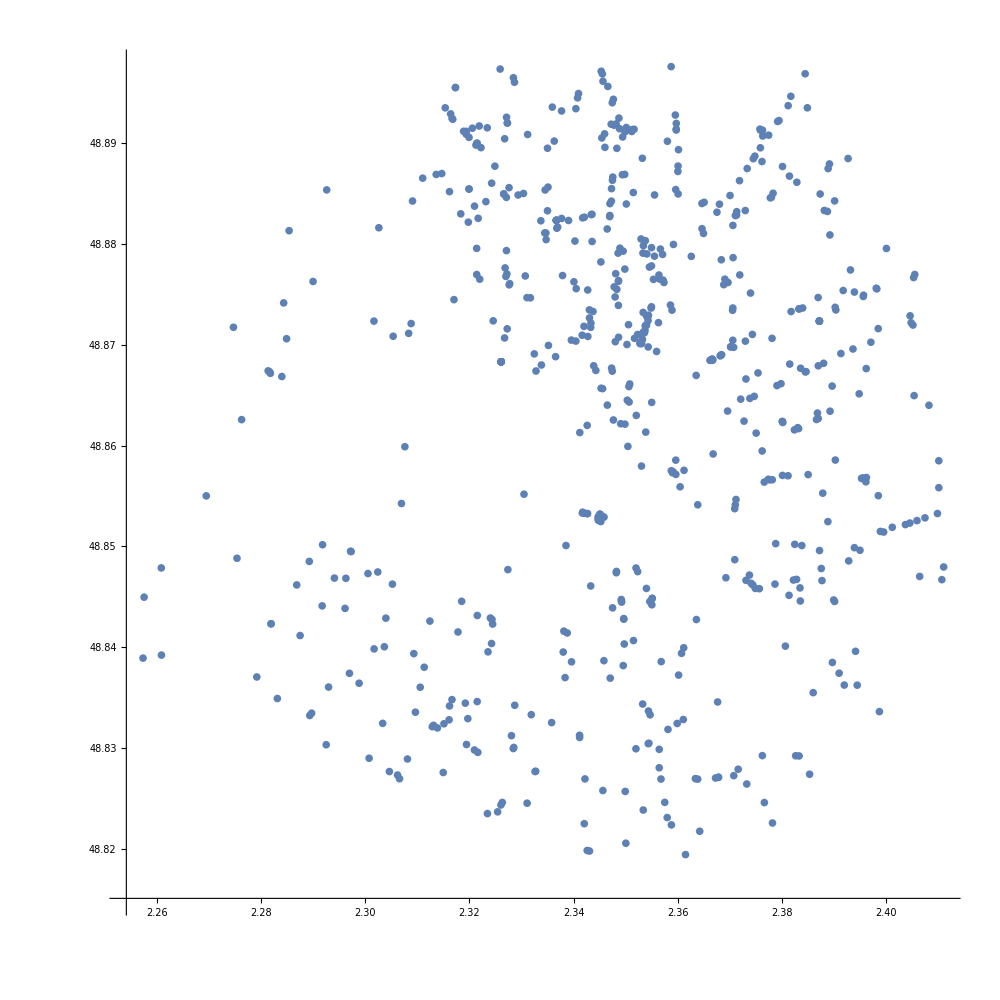

```mathematica
plot=ListPlot[Transpose[{longitude,latitude}],AspectRatio->1,ImageSize->1000,PlotRange->All]
Export[StringJoin[lecteur,adresse,dossierref,"Scrapping-Liste-des-kebab-Paris-BD-Adresse.png"],plot,ImageResolution->300];
Clear[plot];
```

```mathematica
Clear[scrapping2,titrescrapping,data2,data2titre,longitude,latitude,score,scrapping3,titrescrapping2];
```

## Suppression des variables

```mathematica
Clear[dossierdata,dossierref];
Clear[lecteur,adresse];
```